```mathematica
eq=D[u[t,x],t]==-D[u[t,x],{x,3}]+6 u[t,x] D[u[t,x],x];
```

```mathematica
1+1
```

2

```mathematica
ClearAll[u,t,x,c,x0,xmin,xmax,tmax];

c=1;
x0=-10;
xmin=-30;
xmax=30;
tmax=20;

eq=D[u[t,x],t]==-D[u[t,x],{x,3}]+6 u[t,x] D[u[t,x],x];

ic=u[0,x]==(c/2) Sech[(Sqrt[c]/2) (x-x0)]^2;

bc={u[t,xmin]==0,u[t,xmax]==0,Derivative[0,1][u][t,xmin]==0};

sol=NDSolveValue[{eq,ic,bc},u,{t,0,tmax},{x,xmin,xmax}];
```

NDSolveValue::ndsz: t == 0.141348において，刻み幅は実質的にゼロとなります．特異性または硬い系の可能性があります．

NDSolveValue::eerr: 警告：t = 0.141348において独立変数xの方向にスケールされた355134.の局所空間誤差推定が指定の許容誤差範囲を大きく超えています．233ポイントの格子間隔は，希望の精度または確度を達成するには大きすぎる可能性があります．特異性が形成されたかもしれません．もしくはMaxStepSizeまたはMinPointsメソッドオプションを用いてより小さな格子間隔を指定することができます．

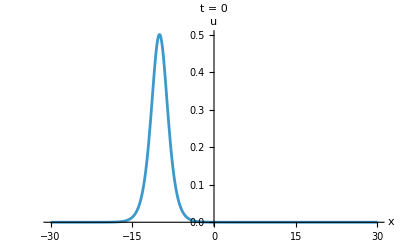

```mathematica
Plot[Evaluate[sol[0,x]],{x,xmin,xmax},PlotRange->All,AxesLabel->{"x","u"},PlotLabel->"t = 0"]
```

```mathematica
Animate[Plot[Evaluate[sol[t,x]],{x,xmin,xmax},PlotRange->{{xmin,xmax},{0,c}},AxesLabel->{"x","u"},PlotLabel->Row[{"KdV soliton, t = ",NumberForm[t,{4,2}]}]],{t,0,tmax}]
```

```mathematica
Plot3D[sol[t,x],{t,0,tmax},{x,xmin,xmax},AxesLabel->{"t","x","u"},PlotRange->All]
```

-Graphics3D-

```mathematica
ClearAll[u,t,x];

xmin=-20;
xmax=20;
tmax=10;

eq=D[u[t,x],t]==-D[u[t,x],{x,3}]+6 u[t,x] D[u[t,x],x];

ic=u[0,x]==Exp[-x^2];

bc=PeriodicBoundaryCondition[u[t,x],x==xmin,TranslationTransform[{xmax-xmin}]];

sol2=NDSolveValue[{eq,ic,bc},u,{t,0,tmax},{x,xmin,xmax},Method->{"MethodOfLines"}];
```

NDSolveValue::femcmsd: 偏微分方程式の空間導関数の階数は2を超えてはなりません．

```mathematica
Animate[Plot[sol2[t,x],{x,xmin,xmax},PlotRange->All,AxesLabel->{"x","u"}],{t,0,tmax}]
```

```mathematica
Animate[Plot[{sol[t,x],uexact[t,x]},{x,xmin,xmax},PlotRange->All,PlotLegends->{"numerical","exact"},AxesLabel->{"x","u"}],{t,0,tmax}]
```